## x-space comparison between HE and FO

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Plots without the FO δ(Q^2) term

### p_T = 88 GeV

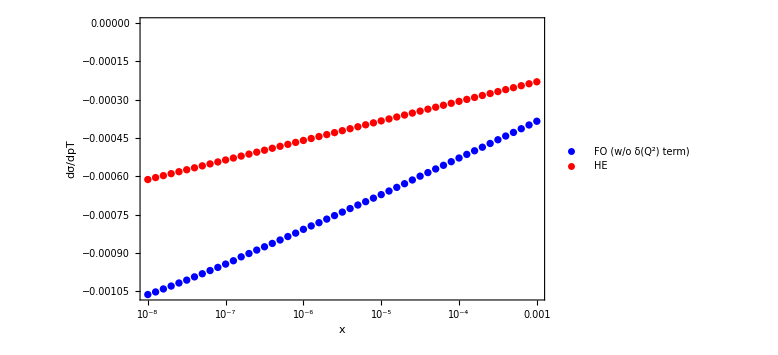

```mathematica
p1 = ListLogLinearPlot[{Import["./datfiles/FO_NLO_pt88.dat","Table"],
Import["./datfiles/HE_NLO_pt88.dat","Table"]},
Frame->True,
FrameStyle->Directive[Black,12],
PlotStyle->{{Thick,Blue},{Thick,Red}},
PlotLegends->LineLegend[{"FO (w/o δ(Q^2) term)","HE"}],
FrameLabel->{{"dσ/dpT",""},{"x", "NLO Contribution at pt=88"}},
PlotRange->{{10^-8,10^-3},All},ImageSize->Large]
```

```mathematica
Export["./plots/fig1.png",p1];
```

Not only the absolute distance between HE and FO increases as x becomes smaller, but also the relative difference increases:

```mathematica
(*at x=0.001*)
Import["./datfiles/FO_NLO_pt88.dat","Table"][[-1,2]]/Import["./datfiles/HE_NLO_pt88.dat","Table"][[-1,2]]
```

1.67251

```mathematica
(*at x=10^-8*)
Import["./datfiles/FO_NLO_pt88.dat","Table"][[1,2]]/Import["./datfiles/HE_NLO_pt88.dat","Table"][[1,2]]
```

1.73561

### p_T = 217 GeV

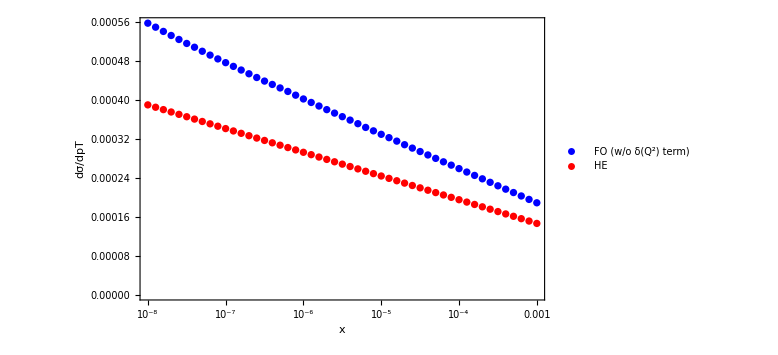

```mathematica
p2 = ListLogLinearPlot[{Import["./datfiles/FO_NLO_pt217.dat","Table"],
Import["./datfiles/HE_NLO_pt217.dat","Table"]},
Frame->True,
FrameStyle->Directive[Black,12],
PlotStyle->{{Thick,Blue},{Thick,Red}},
PlotLegends->LineLegend[{"FO (w/o δ(Q^2) term)","HE"}],
FrameLabel->{{"dσ/dpT",""},{"x", "NLO Contribution at pt=217"}},
PlotRange->{{10^-8,10^-3},All},ImageSize->Large]
```

```mathematica
Export["./plots/fig2.png",p2];
```

Again, not only the absolute distance between HE and FO increases as x becomes smaller, but also the relative difference increases:

```mathematica
(*at x=0.001*)
Import["./datfiles/FO_NLO_pt217.dat","Table"][[-1,2]]/Import["./datfiles/HE_NLO_pt217.dat","Table"][[-1,2]]
```

1.29006

```mathematica
(*at x=10^-8*)
Import["./datfiles/FO_NLO_pt217.dat","Table"][[1,2]]/Import["./datfiles/HE_NLO_pt217.dat","Table"][[1,2]]
```

1.43075